```mathematica
PlotsPath = "/Users/brunogoes/Dropbox/00--Thesis/Figures/Chap4/ToEdit/";
```

## Vectorization☑

```mathematica
(*Easy to call *)
Clear[eye,tp,kp];
eye = IdentityMatrix;
tp = Transpose;
kp = KroneckerProduct;
```

```mathematica
Clear[a,coherentState];
a[Nmax_]:=Transpose[Table[If[i==j+1,Sqrt[i-1],0],{i,1,Nmax},{j,1,Nmax}]];
coherentState[α_,Ν_]:=Table[Exp[-Abs[α]^2/2]*α^n/Sqrt[n!],{n,0,Ν}]/Sqrt[Sum[Exp[-Abs[α]^2]*Abs[α]^(2n)/(n!),{n,0,Ν}]];
```

```mathematica
Clear[jump,unitary2vec,lindblad2vec];
jump [c_]:=kp[c,tp[c†]] ;
unitary2vec[H_]:=With[{ℐ = eye[Length@H]},-ⅈ (kp[H,ℐ]- kp[ℐ,tp[H]])];
lindblad2vec[L_]:=With[{ℐ = eye[Length@L]}, kp[L, tp[L†]]-1/2 kp[(L†.L),ℐ]-1/2 kp[ℐ,tp[L†.L]]];
```

Below is my way of doing the vectorization which used column stacking, it turned out to give different results from the ones Stephen has got

```mathematica
Clear[jump,unitary2vec,lindblad2vec];
jump [c_]:=kp[c*,c] ;
unitary2vec[H_]:=With[{ℐ = eye[Length@H]},-ⅈ (kp[ℐ,H]- kp[Hᵀ,ℐ])];
lindblad2vec[L_]:=With[{ℐ = eye[Length@L]}, kp[L*,L]-1/2 kp[tp[(L†.L)],ℐ]-1/2 kron[ℐ,L†.L]];
```

## Hilbert Space ☑

```mathematica
dim4LS = 4;
dimSource = 4;
dim = dim4LS dimSource^2;
(*Ordering the 4LS basis as:*)
{spinDw,spinUp,trionDw,trionUp} = {{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
```

```mathematica
(*Dipole operators*)
ΣL = Outer[Times, spinDw,trionDw]
ΣR = Outer[Times, spinUp,trionUp]
```

{{0,0,1,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}}

{{0,0,0,0},{0,0,0,1},{0,0,0,0},{0,0,0,0}}

```mathematica
(*Dipole Operators in the large Hilbert Space*)
σL = kp[ΣL, eye[dimSource], eye[dimSource]];
σR = kp[ΣL, eye[dimSource], eye[dimSource]];
```

```mathematica
(*Virtual cavity operators*)
𝕒R = kp[eye[dim4LS],a[dimSource],eye[dimSource]]//N;
𝕒L = kp[eye[dim4LS],eye[dimSource],a[dimSource]]//N;
```

## System and protocol

### System

After passing the first BS the output fields are:

```mathematica
(*1st BS*)
(*Upper path*)
uL = Cos[θ1]𝕒L;
uR = Cos[θ1]𝕒R;

(*Down path*)
dL = ⅈ Sin[θ1]𝕒L ;
dR = ⅈ Sin[θ1]𝕒R;
```

The output field of the upper path is going to interact with the 4LS:

```mathematica
(*Light-matter interaction Hamiltonian for the upper path*)
h0 = ΔL σL†.σL+ΔR σR†.σR;
hI = -ⅈ (√ηlm √(γ η κ))/2(σL†.uL - uL†.σL + σR†.uR - uR†.σR);
h = h0 + hI ;
```

```mathematica
(*Output modes*)
Loutu = √ηd(√γ σL+√(η κ)uL);
Routu = √ηd(√γ σR+√(η κ)uR);
Loutd = √ηd(√(η κ)dL);
Routd = √ηd(√(η κ)dR);
```

Recombination at the BS:

```mathematica
(*Interference in the 2nd BS*)
RoutD1=Routu Cos[θ2]+ⅈ Routd Exp[ⅈ φ] Sin[θ2];
LoutD1=Loutu Cos[θ2]+ⅈ Loutd Exp[ⅈ φ] Sin[θ2];

RoutD2=Routd Exp[ⅈ*φ] Cos[θ2]+ⅈ Routu Sin[θ2];
LoutD2=Loutd Exp[ⅈ*φ] Cos[θ2]+ⅈ Loutu Sin[θ2];
```

### Superoperators

```mathematica
PrettyTiming[ℋ = unitary2vec[h]]
```

0h : 0m : 6s

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4091,0.+0. ⅈ,0.+0. ⅈ},4094,{1}}
 |  |  |  |

```mathematica
PrettyTiming[𝒟γ=lindblad2vec[Loutu]+lindblad2vec[Routu]+lindblad2vec[Loutd]+lindblad2vec[Routd]+(1-η)κ(lindblad2vec[𝕒R]+lindblad2vec[𝕒L]);]
```

0h : 1m : 14s

```mathematica
(* System decay with correlation due to cascaded coupling *)
PrettyTiming[𝒟γs=γs lindblad2vec[σL†.σL]+γs lindblad2vec[σR†.σR]+κs lindblad2vec[𝕒L†.𝕒L]+κs lindblad2vec[𝕒R†.𝕒R];](* System (γs) and input (κs) dephasing *)
```

0h : 0m : 47s

```mathematica
PrettyTiming[𝒥ηd=-ηRD1 jump[RoutD1]-ηRD2 jump[RoutD2]-ηLD1 jump[LoutD1]-ηLD2 jump[LoutD2];(* Conditional evolution *)]
```

0h : 0m : 43s

```mathematica
ℒ = ℋ + 𝒟γ + 𝒟γs +𝒥ηd
```

{{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,4091,0.+0. ⅈ,0.+0. ⅈ},4094,{1}}
 |  |  |  |

```mathematica
Dimensions@ℒ
Head@ℒ
```

{4096,4096}

List

## Fock-space exploration to dimension reduction - I want to discuss

```mathematica
(* Choose a parameter set to explore the Fock-Liouville space *)
par={
ΔL->0,ΔR->0, (* Detunings *)
γ->1,κ->0.01,(* Decay rates *)
η->0.9,ηlm->0.9,ηd->0.9,(* Input/coupling efficiency *)
ηRD1->0.5,ηRD2->0.5,ηLD1->0.5,ηLD2->0.5,(* Detector efficiency/conditional evolution parameters *)
γs->0.1,κs->0.1,(* Dephasing *)
φ->0.235,(* interferometer phase *)
θ1->0.412,θ2->0.12(* Beam splitter ratios *)
};
```

Is it a number? Did I forget to substitute some variable?

```mathematica
Total[Flatten[ℒ/.par]]
```

-3023.86+0. ⅈ

Why is this a H-polarized input coherent state?
I would expect something like kp[{1,1,0,0},{1,1,1,1},{1,1,1,1}] instead...

```mathematica
(* Choose an initial state to reduce the necessary subspace: gs spin superposition + H-polarized input coherent state (up to 3 photons) *)
istate=Flatten[kp[{1,1,0,0},{1,1,1,1},{1,0,0,0}]];
istate=Flatten[kp[istate,istate]];
```

```mathematica
aux1 = Sign[istate]*Range[dim^2];(*Sign of initial state assigns 1 to positive values, 0 when the value is 0 and -1 when the value is negative. Range[Dim2] makes a big list going from 1 to 4096. The output is a list with a bunch of zeros and the indexes of the initial nodes where the values are not zero.*)
```

```mathematica
initialnodes=DeleteCases[aux1,0];(*every place where the value of aux 1 is zero are neglected*)
```

```mathematica
%
```

{1,5,9,13,17,21,25,29,257,261,265,269,273,277,281,285,513,517,521,525,529,533,537,541,769,773,777,781,785,789,793,797,1025,1029,1033,1037,1041,1045,1049,1053,1281,1285,1289,1293,1297,1301,1305,1309,1537,1541,1545,1549,1553,1557,1561,1565,1793,1797,1801,1805,1809,1813,1817,1821}

```mathematica
Head@%
Dimensions@%%
```

List

{64}

This step I don’t really understand what is the purpose...

```mathematica
aux2= NumericQ/@Flatten[ℒ+x*eye[Length[ℒ]]]/.{True->0,False->1}
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,16777170,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1}
 |  |  |  |

```mathematica
Head@%
Dimensions@%%
```

List

{16777216}

But it is clearly crucial to build the adjacency matrix...

```mathematica
adjacencymatrix=Partition[aux2,dim^2];
```

```mathematica
Head@%
Dimensions@%%
```

List

{4096,4096}

```mathematica
aux3=Transpose[Sign[adjacencymatrix+Transpose[adjacencymatrix]]]
```

{1}
 |  |  |  |

```mathematica
Head@%
Dimensions@%%
```

List

{4096,4096}

```mathematica
AdjacencyGraph[aux3,
VertexStyle->Table[i->If[MemberQ[initialnodes,Range[dim^2][[i]]],Red,Black],{i,dim^2}],
PlotLabel->"Full Fock-Liouville space and intereactions for the ME",
Frame->True,
FrameLabel->{"Red dot is the initial state"}]
```

```mathematica
(* This applies the propagator once to see which Fock-Liouville states become populated *)
expState=Sign[Abs[MatrixExp[ℒ/.par].istate]];
```

```mathematica
aux4=expState*Range[dim^2];(*Encontrando os indexes*)
```

```mathematica
(* Let's now look at all the Fock-Liouville basis vectors that were explored *)
nodeset=DeleteCases[aux4,0];
```

```mathematica
nodeset
```

{1,2,3,4,5,6,7,9,10,13,17,21,25,29,33,34,35,37,38,41,65,66,67,68,69,70,71,73,74,77,81,85,89,93,97,98,99,101,102,105,129,130,131,132,133,134,135,137,138,141,145,149,153,157,161,162,163,165,166,169,193,194,195,196,197,198,199,201,202,205,209,213,217,221,225,226,227,229,230,233,257,258,259,260,261,262,263,265,266,269,273,277,281,285,289,290,291,293,294,297,321,322,323,324,325,326,327,329,330,333,337,341,345,349,353,354,355,357,358,361,385,386,387,388,389,390,391,393,394,397,401,405,409,413,417,418,419,421,422,425,513,514,515,516,517,518,519,521,522,525,529,533,537,541,545,546,547,549,550,553,577,578,579,580,581,582,583,585,586,589,593,597,601,605,609,610,611,613,614,617,769,770,771,772,773,774,775,777,778,781,785,789,793,797,801,802,803,805,806,809,1025,1026,1027,1028,1029,1030,1031,1033,1034,1037,1041,1045,1049,1053,1057,1058,1059,1061,1062,1065,1281,1282,1283,1284,1285,1286,1287,1289,1290,1293,1297,1301,1305,1309,1313,1314,1315,1317,1318,1321,1537,1538,1539,1540,1541,1542,1543,1545,1546,1549,1553,1557,1561,1565,1569,1570,1571,1573,1574,1577,1793,1794,1795,1796,1797,1798,1799,1801,1802,1805,1809,1813,1817,1821,1825,1826,1827,1829,1830,1833,2049,2050,2051,2052,2053,2054,2055,2057,2058,2061,2065,2069,2073,2077,2081,2082,2083,2085,2086,2089,2113,2114,2115,2116,2117,2118,2119,2121,2122,2125,2129,2133,2137,2141,2145,2146,2147,2149,2150,2153,2177,2178,2179,2180,2181,2182,2183,2185,2186,2189,2193,2197,2201,2205,2209,2210,2211,2213,2214,2217,2305,2306,2307,2308,2309,2310,2311,2313,2314,2317,2321,2325,2329,2333,2337,2338,2339,2341,2342,2345,2369,2370,2371,2372,2373,2374,2375,2377,2378,2381,2385,2389,2393,2397,2401,2402,2403,2405,2406,2409,2561,2562,2563,2564,2565,2566,2567,2569,2570,2573,2577,2581,2585,2589,2593,2594,2595,2597,2598,2601}

```mathematica
nodeset//Dimensions
```

{400}

```mathematica
aux5=tp[Sign[adjacencymatrix+tp[adjacencymatrix]]]
```

{1}
 |  |  |  |

```mathematica
aux6 = aux5[[nodeset,nodeset]]
```

{1}
 |  |  |  |

```mathematica
Head@%
Dimensions@%%
```

List

{400,400}

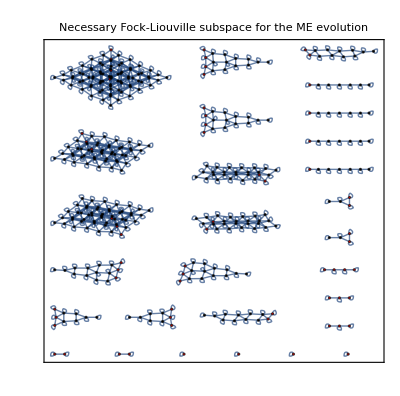

```mathematica
AdjacencyGraph[aux6,
VertexStyle->Table[i->If[MemberQ[initialnodes,nodeset[[i]]],Red,Black],{i,Length[nodeset]}],PlotLabel->"Necessary Fock-Liouville subspace for the ME evolution",
Frame->True,
FrameLabel->{"Red dots are the initial state"}]
Export[PlotsPath<>"NecessaryFockLiouvilleSpace.pdf",%];
```

## Generating data and plots

```mathematica
(* Building the necessary subspace using this information *)
ℒSS=ℒ[[nodeset,nodeset]];
istateSS=istate[[nodeset]];
traceSS=Flatten[eye[dim]][[nodeset]];
```

```mathematica
Head@ℒSS
Dimensions@ℒSS
Head@istateSS
Dimensions@istateSS
Head@traceSS
Dimensions@traceSS
```

List

{400,400}

List

{400}

List

{400}

```mathematica
outset=ParallelTable[
effN=1;
dephN=0;
par={
ΔL->0,ΔR->0, (* Detunings *)
γ->1,κ->10^k,(* Decay rates *)
η->effN,ηlm->1,ηd->1,(* Input/coupling efficiency *)
ηRD1->0.,ηRD2->0.,ηLD1->0.,ηLD2->0.,(* Detector efficiency/conditional evolution parameters *)
γs->dephN,κs->0dephN,(* Dephasing *)
φ->0,(* interferometer phase *)
θ1->0,θ2->0
};

traceSS=Flatten[eye[dim]][[nodeset]];
σupdown={{0,1,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,0}};
σupdown=kp[σupdown,eye[dimSource],eye[dimSource]];
σupdown=kp[σupdown,eye[dim]][[nodeset,nodeset]];

istate=Flatten[kp[{1,1,0,0}/Sqrt[2],{1,1,0,0}/Sqrt[2],{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
phtOut12=traceSS.σupdown.MatrixPower[MatrixExp[ℒSS/.par],100000000].istate;

istate=Flatten[kp[{1,1,0,0}/Sqrt[2],{0,1,0,0},{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
phtOut=traceSS.σupdown.MatrixPower[MatrixExp[ℒSS/.par],100000000].istate;

istate=Flatten[kp[{1,1,0,0}/Sqrt[2],coherentState[1/Sqrt[2],3],{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
cohOut12=traceSS.σupdown.MatrixPower[MatrixExp[ℒSS/.par],100000000].istate;

istate=Flatten[kp[{1,1,0,0}/Sqrt[2],coherentState[1,3],{1,0,0,0}]];
istate=Flatten[kp[istate,istate]][[nodeset]];
cohOut=traceSS.σupdown.MatrixPower[MatrixExp[ℒSS/.par],100000000].istate;

par={
ΔL->0,ΔR->0, (* Detunings *)
γ->1,κ->10^k,(* Decay rates *)
η->effN,ηlm->1,ηd->1,(* Input/coupling efficiency *)
ηRD1->0.,ηRD2->0.,ηLD1->0.,ηLD2->0.,(* Detector efficiency/conditional evolution parameters *)
γs->dephN,κs->0dephN,(* Dephasing *)
φ->0,(* interferometer phase *)
θ1->π/4,θ2->π/4
};

tsplit=2;
Dset={ηRD1->1,ηRD2->0,ηLD1->1,ηLD2->0};

istate=Flatten[kp[{Cos[θ],Sin[θ],0,0},{0,1,0,0},{1,0,0,0}]]/.par;
istate=Flatten[kp[istate,istate]][[nodeset]];
prPht=1-traceSS.MatrixPower[MatrixExp[ℒSS/.Dset/.par],100000000].istate;
(*
istate=Flatten[KP[{Cos[θ],Sin[θ],0,0},cohstateAppx[1.038,3],{1,0,0,0}]]/.par;
istate=Flatten[KP[istate,istate]][[nodeset]];
prCoh=1-traceSS.MatrixPower[MatrixExp[LiouSS/.κs->0/.Dset/.par],20000].istate;

{x,Sqrt[(prCoh/.θ->0)(prCoh/.θ->π/2)]+Sqrt[(1-prCoh/.θ->0)(1-prCoh/.θ->π/2)],
Sqrt[(prPht/.θ->0)(prPht/.θ->π/2)]+Sqrt[(1-prPht/.θ->0)(1-prPht/.θ->π/2)]}
*)

{k,phtOut12,cohOut12,Sqrt[(prPht/.θ->0)(prPht/.θ->π/2)]+Sqrt[(1-prPht/.θ->0)(1-prPht/.θ->π/2)],phtOut,cohOut},{k,-5,2,0.1}];
```

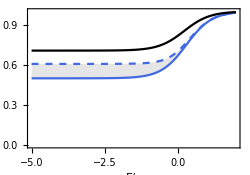

```mathematica
ListPlot[{{#1,2Abs[#2]}&@@@outset,{#1,2Abs[#3]}&@@@outset,{#1,#4//Re}&@@@outset},
PlotRange->{0.,1},
Joined->True,PlotStyle->{{ColorData["HTML","RoyalBlue"]},{ColorData["HTML","RoyalBlue"],Dashed},ColorData["HTML","Black"],{ColorData["HTML","RoyalBlue"]},{ColorData["HTML","RoyalBlue"],Dashed}},Filling->1->{2},
Frame->True,
BaseStyle->14,
AspectRatio->0.7,
AxesOrigin->{-5,0},
FillingStyle->{Opacity[0.2,Gray],Opacity[0.2,Gray]},FrameLabel->{"Γ/γ",""},
ImageSize->250
]
Export[PlotsPath<>"cBhatIdealcase.pdf",%];
```